```mathematica
Expand[(((x2-x1)/V)^2-((√(h^2+x2^2))^2+(√(h^2+x2^2))^2))/(-2(√(h^2+x2^2))*(√(h^2+x1^2)))]
Simplify[(x1 x2)/(V^2 √(h^2+x1^2) √(h^2+x2^2))+x2^2/(√(h^2+x1^2) √(h^2+x2^2))-x2^2/(2 V^2 √(h^2+x1^2) √(h^2+x2^2))]
TrigReduce[]
```

h^2/(√(h^2+x1^2) √(h^2+x2^2))-x1^2/(2 V^2 √(h^2+x1^2) √(h^2+x2^2))+(x1 x2)/(V^2 √(h^2+x1^2) √(h^2+x2^2))+x2^2/(√(h^2+x1^2) √(h^2+x2^2))-x2^2/(2 V^2 √(h^2+x1^2) √(h^2+x2^2))

(x2 (2 x1+(-1+2 V^2) x2))/(2 V^2 √(h^2+x1^2) √(h^2+x2^2))

ArcCos[(x2 (2 x1+(-1+2 V^2) x2))/(2 V^2 √(h^2+x1^2) √(h^2+x2^2))]

```mathematica
Plot[ArcCos[(x2 (2 x1+(-1+2 V^2) x2))/(2 V^2 √(h^2+x1^2) √(h^2+x2^2))]/.{V->1,h->2},{x1}]
```

```mathematica
Clear["Global`*"]
H2=√(h^2+x2^2);
H1=√(h^2+x1^2);
x2=x1+ΔT*v;
 ArcCos[(ΔT^2-(H2^2+H1^2))/(-2 H2*H1)]
Plot[ ArcCos[(ΔT^2-(H2^2+H1^2))/(-2 H2*H1)]/.{h->1,v->1,ΔT->0.001},{x1,-1,4}]
NIntegrate[ArcCos[(ΔT^2-(H2^2+H1^2))/(-2 H2*H1)]/.{h->1,v->1,x1->11},{ΔT,0,1}]
```

ArcCos[-(-2 h^2-x1^2+ΔT^2-(x1+v ΔT)^2)/(2 √(h^2+x1^2) √(h^2+(x1+v ΔT)^2))]

1045001

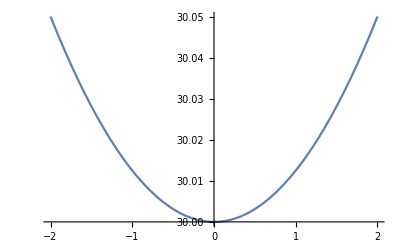

{{a→0.-26.4575 ⅈ,d→41.5594-25.742 ⅈ},{a→0.+26.4575 ⅈ,d→-41.5594-25.742 ⅈ}}

```mathematica
Plot[10Cosh[x/20]+20,{x,-2,2}]
NSolve[{
80==2 a √(Cosh[d/a]^2) Tanh[d/a],
50==a Cosh[d/a]+20}]/.C[1]->0
```

```mathematica
√(1+(D[a Cosh[x/a]+20,x])^2)
```

√(1+Sinh[x/a]^2)

```mathematica
50==∫√(1+Sinh[x/a]^2)ⅆx
```

```mathematica
80==2 a √(Cosh[d/a]^2) Tanh[d/a]
```

50==2 a √(Cosh[d/a]^2) Tanh[d/a]

```mathematica
4
```

$Aborted

```mathematica
√(1+(D[a Cosh[x/a],x])^2)
```

√(1+Sinh[x/a]^2)

```mathematica
Solve[2 R^2-2 R^2 Cos[θ]==s^2,R]


r^2+R^2-2 r R*Cos[θ/2]==(s/2)^2/.R->s/(√2 √(1-Cos[θ]))
```

{{R→-s/(√2 √(1-Cos[θ]))},{R→s/(√2 √(1-Cos[θ]))}}

r^2+s^2/(2 (1-Cos[θ]))-(√2 r s Cos[θ/2])/(√(1-Cos[θ]))==s^2/4

```mathematica
{{R->-s/(√2 √(1-Cos[θ]))},{}}
```

r^2+R^2-2 r R Cos[θ/2]==s^2/4

```mathematica
R->s/(√2 √(1-Cos[θ]))
Solve[r^2+s^2/(2 (1-Cos[θ]))-(√2 r s Cos[θ/2])/(√(1-Cos[θ]))==s^2/4,r]
```

R→s/(√2 √(1-Cos[θ]))

{{r→1/2 (-√(s^2-(2 s^2)/(1-Cos[θ])+(2 s^2 Cos[θ/2]^2)/(1-Cos[θ]))+(√2 s Cos[θ/2])/(√(1-Cos[θ])))},{r→1/2 (√(s^2-(2 s^2)/(1-Cos[θ])+(2 s^2 Cos[θ/2]^2)/(1-Cos[θ]))+(√2 s Cos[θ/2])/(√(1-Cos[θ])))}}

```mathematica
(s/(√2 √(1-Cos[θ])))/(1/2 (√(s^2-(2 s^2)/(1-Cos[θ])+(2 s^2 Cos[θ/2]^2)/(1-Cos[θ]))+(√2 s Cos[θ/2])/(√(1-Cos[θ]))))
(s/(√2 √(1-Cos[θ])))/(1/2 (√(s^2-(2 s^2)/(1-Cos[θ])+(2 s^2 Cos[θ/2]^2)/(1-Cos[θ]))+(√2 s Cos[θ/2])/(√(1-Cos[θ]))))
```

```mathematica
Sec[θ/2]/.θ->(360/n)°/.n->{1,2,3,4,5,6,7,8,9,10}
```

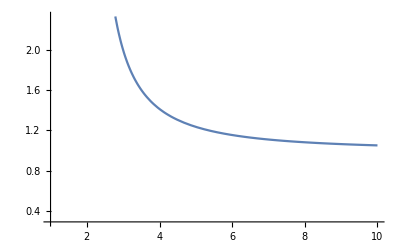

```mathematica
Plot[Sec[(180 °)/n],{n,1,10}]
```

```mathematica
√(s^2*(1-Cos[θ])/(1-Cos[θ])-(2 s^2)/(1-Cos[θ])+(2 s^2 Cos[θ/2]^2)/(1-Cos[θ]));
√((s^2*(1-Cos[θ]) - 2 s^2+2 s^2 Cos[θ/2]^2)/(1-Cos[θ]));
s √(((1-Cos[θ]) - 2 +2  Cos[θ/2]^2)/(1-Cos[θ]));
s √((-1+2  Cos[θ/2]^2-Cos[θ])/(1-Cos[θ]));
s √((-1+(1+Cos[θ])-Cos[θ])/(1-Cos[θ]));
s √(0/(1-Cos[θ]));
s*√0;
0;
```

```mathematica
(s/(√2 √(1-Cos[θ])))/(1/2 (√(s^2-(2 s^2)/(1-Cos[θ])+(2 s^2 Cos[θ/2]^2)/(1-Cos[θ]))+(√2 s Cos[θ/2])/(√(1-Cos[θ]))));
(s/(√2 √(1-Cos[θ])))/(1/2 (0+(√2 s Cos[θ/2])/(√(1-Cos[θ]))));
(s/(√2 √(1-Cos[θ])))/(1/2 (√2 s Cos[θ/2])/(√(1-Cos[θ])));
(s*2 √(1-Cos[θ]))/(√2 √(1-Cos[θ])*√2 s Cos[θ/2]);
1/Cos[θ/2];
Sec[θ/2];
```

Sec[θ/2]

```mathematica
2
```

```mathematica
Sec[(180°)/n]/.n->{3,4,5,6,7,8,9,10}//N
```

{2.,1.41421,1.23607,1.1547,1.10992,1.08239,1.06418,1.05146}